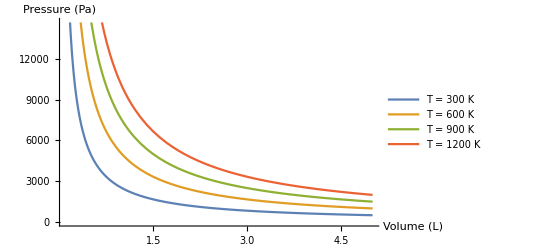

```mathematica
(* Ideal Gas Law and State Variables *)
R=8.314;
n=1;
P[V_,T_]:=n R T/V;

(* Plot P vs V for different T *)
Plot[Evaluate[Table[P[V,T],{T,{300,600,900,1200}}]],{V,0.1,5},PlotLegends->Placed[{"T = 300 K","T = 600 K","T = 900 K","T = 1200 K"},Above],AxesLabel->{"Volume (L)","Pressure (Pa)"}]
```

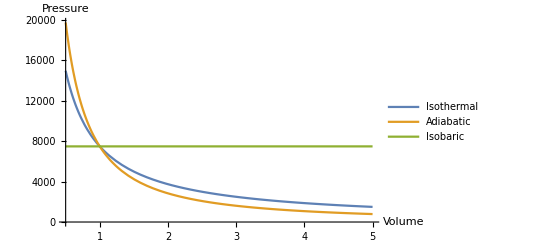

```mathematica
(* PV Diagrams for Common Thermodynamic Processes *)
T=900;gamma=1.4;V0=1;
P0=P[V0,T];
adiabatic[V_]:=P0 (V0/V)^1.4;
isothermal[V_]:=P0 (V0/V);
isobaric[V_]:=P0;

Plot[{isothermal[V],adiabatic[V],isobaric[V]},{V,0.5,5},PlotLegends->{"Isothermal","Adiabatic","Isobaric"},AxesLabel->{"Volume","Pressure"}]
```

```mathematica
(* Heat Equation *)
heqn=D[u[x,t],t]==D[u[x,t],{x,2}];

(* Initial condition *)
ic=u[x,0]==E^(-x^2);

(* Solve *) 
sol=DSolveValue[{heqn,ic},u[x,t],{x,t}]
Plot3D[sol,{x,-5,5},{t,0,2},AxesLabel->{"x","t","u"},PlotRange->All, Mesh->None,PlotPoints->100]
```

(ⅇ^(-x^2/(1+4 t)))/(√(1+4 t))

-Graphics3D-

```mathematica
(* Efficiency *)
carnotEfficiency[Tc_,Th_]:=1-Tc/Th
ottoEfficiency[r_,gamma_]:=1-1/r^(gamma-1)
dieselEfficiency[r_,rc_,gamma_]:=1-(1/r^(gamma-1))*((rc^gamma-1)/(gamma*(rc-1)))

Manipulate[Module[{ηCarnot,ηOtto,ηDiesel,labels,colors},
ηCarnot=carnotEfficiency[Tc,Th];
ηOtto=ottoEfficiency[r,γ];
ηDiesel=dieselEfficiency[r,rc,γ];BarChart[{ηCarnot,ηOtto,ηDiesel},ChartLabels->{"Carnot","Otto","Diesel"},ChartStyle->{Blue,Red,Green},PlotRange->{0,1},BarSpacing->0.25,ImageSize->Medium]],{{Th,500,"T_H (K)"},400,1000},{{Tc,300,"T_C (K)"},300,500},{{r,5,"Compression Ratio r"},1.1,20,Appearance->"Labeled"},{{rc,2,"Cutoff Ratio rc (Diesel only)"},1.01,5,Appearance->"Labeled"},{{γ,1.4,"Gamma (γ = cp/cv)"},1.01,2,Appearance->"Labeled"}]
```

```mathematica
(* Statistical Physics *)
Manipulate[Module[{fMB,fBE,fFD,energies,plotMB,plotBE,plotFD},energies=Range[0.01,10,0.05];
k=1;
fMB[Energy_]:=Exp[-(Energy-μ)/(k T)];
fBE[Energy_]:=1/(Exp[(Energy-μ)/(k T)]-1);
fFD[Energy_]:=1/(Exp[(Energy-μ)/(k T)]+1);
plotMB=Plot[fMB[Energy],{Energy,0.01,10},PlotStyle->{Dashed,Black},PlotLabel->Style["Maxwell-Boltzmann Distribution",14,Bold],AxesLabel->{"E","f_MB(E)"},PlotRange->{0,1},ImageSize->Medium];
plotBE=Plot[fBE[Energy],{Energy,Max[μ+0.001,0.01],10},PlotStyle->{Blue},PlotLabel->Style["Bose-Einstein Distribution",14,Bold],AxesLabel->{"E","f_BE(E)"},PlotRange->{0,1},ImageSize->Medium];
plotFD=Plot[fFD[Energy],{Energy,0.01,10},PlotStyle->{Red},PlotLabel->Style["Fermi-Dirac Distribution",14,Bold],AxesLabel->{"E","f_FD(E)"},PlotRange->{0,1},ImageSize->Medium];
Column[{plotMB,plotBE,plotFD},Spacings->2]],{{T,1,"Temperatur T"},0.1,5,Appearance->"Labeled"},{{μ,5,"Potensial Kimia μ"},-10,10,Appearance->"Labeled"}]
```